```mathematica
or2Lis[expr_]:={#}&/@(expr/.{or[a__]->{a}})
```

```mathematica
or2Lis[or[p,q]]
```

{{p},{q}}

```mathematica
makeNewLis[expr]
```

{or[p,q],or[p,not[q]],not[p],not[q]}

```mathematica
or2Lis/@makeNewLis[expr]
```

{{{p},{q}},{{p},{not[q]}},not[{p}],not[{q}]}

```mathematica
Map[Length,{{{p},{q}},{{p},{not[q]}},not[{p}],not[{q}]},{1}]
```

{2,2,1,1}

```mathematica
Clear[B]
```

## Input

A

(B∨C∨D)

## output

```mathematica
Clear[B];form[head_,tail_]:=(for[head]->#&/@(for/@tail))
```

```mathematica
form[¬A,{B,C,D}]
```

```mathematica
Sequence@@(fo[!A]->#1&)/@fo/@{B,C,D}
```

Sequence[¬A→B,¬A→C,¬A→D]

```mathematica
Sequence@@(fo[!A]->#1&)/@fo/@{B,C,D}
```

Sequence[¬A→B,¬A→C,¬A→D]

```mathematica
{for[A]->for[B],for[A]}
```

## web

```mathematica
web[{1,2,3},{1,2,3}]
```

{for[1]→for[1],for[1]→for[2],for[1]→for[3],for[2]→for[1],for[2]→for[2],for[2]→for[3],for[3]→for[1],for[3]→for[2],for[3]→for[3]}

```mathematica
Clear[former,web,B]
former[layer2_][head_]:=(for[head]->#&/@(for/@layer2)); 
web[layer1_,layer2_]:=Module[{},Flatten[former[layer2][#]&/@layer1]]
thread[layer1_,layer2_]:=pbcopy[StringReplace[ToString[web[layer1,layer2]],"for"->"fo"]]
```

```mathematica
thread[{1,2},{3,4,5}]
```

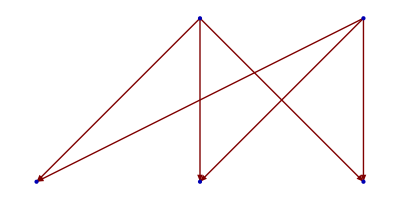

```mathematica
LayeredGraphPlot@{for[A]->for[B],for[A]->for[C],for[A]->for[D],for[X]->for[B],for[X]->for[C],for[X]->for[D]}
```

```mathematica
{for[A]->for[B],for[A]->for[C],for[A]->for[D],for[X]->for[B],for[X]->for[C],for[X]->for[D]}
```

```mathematica
1
```

```mathematica
1
```

```mathematica
{for[A]->for[B],for[A]->for[C],for[A]->for[D],for[X]->for[B],for[X]->for[C],for[X]->for[D]}
```

```mathematica
{for[A]->for[B],for[A]->for[C],for[A]->for[D],for[X]->for[B],for[X]->for[C],for[X]->for[D]}
```

```mathematica
web[{A,X},{B,C,D}]
```

```mathematica
web[{A,X},{B,C,D}]
```

```mathematica
web[{A,X},{B,C,D}]
```

```mathematica
"echo \""<>ToString[{for[A]->for[B],for[A]->for[C],for[A]->for[D],for[X]->for[B],for[X]->for[C],for[X]->for[D]}]<>"\" | pbcopy"]
```

```mathematica
execute["echo \"{for[A] -> for[B], for[A] -> for[C], for[A] -> for[D], for[X] -> for[B], for[X] -> for[C], for[X] -> for[D]}\" | pbcopy"]
```

```mathematica
1
```

1

```mathematica
pbcopy["hello world"]
```

```mathematica
L
```

```mathematica
execute["b40"]
```

b
[H[2J]2;brightness .4.07]1;.07

```mathematica
string="echo \"{for[A] -> for[B], for[A] -> for[C], for[A] -> for[D], for[X] -> for[B], for[X] -> for[C], for[X] -> for[D]}\" | pbcopy";
```

```mathematica
1
```

1

```mathematica
pbcopy[string]
```

```mathematica
{for[A]->for[B],for[A]->for[C],for[A]->for[D],for[X]->for[B],for[X]->for[C],for[X]->for[D]}
```

```mathematica
1
```

1

```mathematica
st
```

```mathematica
pbcopy[string_]:=Module[
{file,output},
DeleteFile["~/_2______________.sh"];
file=CreateFile["~/_2______________.sh"];
WriteString[file,"#!/usr/local/bin/zsh

\n"<>string<>""];
RunProcess["/usr/local/bin/zsh","StandardOutput","chmod a+x "<>file];
output=RunProcess["/usr/local/bin/zsh","StandardOutput",file];
Print[output]
]
```

{1,2}